この部分は修正をnbの保存するときに実行します。（メインテナー向き)

```mathematica
saveC[]
```

Saved in C:\Users\yuya\Desktop\initAndPackages\raytrace2D_180523-125550.nb.

この部分は、パッケージをインストールするときに実行します。初期化セルを実行するかどうかの質問にはYesと答えて下さい。インストールの結果、Users/XXX/Appdata/Roaming/Mathematica/Applications/に
*.mxのファイルが作られ、<<で読み取り可能になります。
??*`でHelpがでます。
*は下の、{}に入っている文字列（パッケージ名)が入ります。

```mathematica
DumpSave[FileNameJoin[{$UserBaseDirectory,"Applications","rayTrace2D.mx"}],"rayTrace2D`"]
```

{rayTrace2D`}

パッケージを読み込んだ後、??パッケージ名`* で、ヘルプが出ます。この時、 <<ファイル名` であり、??パッケージ名`で、両者は揃っていない場合も有ることに注意して下さい。

```mathematica
ClearAll["rayTrace2D`*"]
```

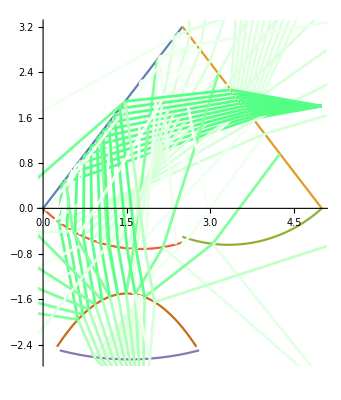

```mathematica
rayTrace[]
```

```mathematica
<<rayTrace2D`
??"rayTrace2D`*"
```

### 光線追跡二次元モジュール ver.2.0

２次元の境界面での屈折反射を計算する。
rayTrace[boundary, ray, recursive] : レイトレース計算を再帰的に行い、Graphicsオブジェクトを出力する。
refract[normal-vector, ray-vector] ：交点とその法線ベクトルを元に、光線の反射屈折ベクトル及び、反射率を返す。
crossLine : lineとrayの交点（で最も光線の始点に近いもの）を求め、交点と、そこでの境界面の法線ベクトルを返す。
crossArc : 円弧lineとrayの交点を求め、交点と、そこでの境界面の法線ベクトルを返す。
crossPoint : 関数曲線(func型)とrayの交点を求め、交点と、そこでの境界面の法線ベクトルを返す。
v2p : v(境界データ)　から、parametricな座標値{x[t],y[t]}の表式を、parametricへの代入規則で返す。
v2f :  v(境界データ)　から、f[x,y]==0 な描画式を返す。但し、==0の部分は返さない。「多分使っていない」
v2θc: v(arcの境界データ)から、arcの中心点(center), その始点終点の位相角(start, end)を返す。

残った実装。(boundaryに指定されたreflectivityなどがrefractに渡っていない？)

```mathematica
BeginPackage["rayTrace2D`"];
```

```mathematica
rayTrace::usage="光線追跡を二次元でおこなう。 rayTrace[boundary, ray, recursivecount, options]\n光線が最初に接触する境界を探し、そこまでの線分を描くグラフィックス情報を返すと同時に、\nそこでの反射屈折を計算して、再帰的に自分を読み出す。\n無限再帰にならないよう、再帰的に呼び出すネストの深さの最大値はrecursivecountで制限する。\n
rayTrace[]でデモを実行。(??rayTraceで中身をみることができる）\n
boundary: 境界面データ。 代入規則・順不同のリスト形式で、基本形は{type → \"line\"|\"arc\"|\"func\", opts}。\"line\"は線分データ、\"arc\"は円弧データ、\"func\"は任意関数データ。これらを複数含むリスト。
opts:
\tTraditionalForm`pos → {x, \ y} : 原点座標。境界の描画開始点。 (\"line\", \"arc\"で必須)
\tTraditionalForm`vec→{x, \ y}\ : 描画ベクトル。pos + vecで描画終了点。(\"line\", \"arc\"で必須)
\triTraditionalForm` : 屈折率。境界面の法線ベクトル　(vecを90度みだり回転したもの)が指す方が n
\tTraditionalForm`cuv → \ C : 曲率。\"arc\"で必須。円弧の半径TraditionalForm`rとの関係は TraditionalForm`r == 1/Cで、法線方向に膨らむときは正、逆方向で負となる。
\tfunction → Function[{x,y},.....] : type==\"func\"の時に必須。純関数fを指定し、f==0が境界の描画方程式となるようにする。
\tparametric → {Function[{t},fx[...]],Function[{t},fy[...]]} : type==\"func\"の時に必須。tを媒介変数とするParametricな関数ベクトルを指定し、t==0が始点、t==1が終点となるように設定する。
\treflectivity → R : 境界面の反射率(0-1)。フレネル反射を無視して、強制的にこの反射利を利用する。
\tabsorbance → A : 境界面の吸収率。入射光は強制的にこれだけの光を減衰する。(0-1)。\n
ray: 光線データ。type → \"ray\"で、{pos → {x,y}, vec → {xd,yd}, opts}で与える。
opts:
\tpow → Number : 光線の強度。デフォルトは1。
\tπpowerFraction → [0..1] : π偏光の強度での含有率。
\tσpowerFraction → [0..1] : σ偏光の強度での含有率。
\tcolor → Number : 光の描画時の色。LCHColorのhを指定する。\n
recursivecount: 再帰で呼び出す毎にここでの数値を一つ減らしてrayTraceを呼び出すようになっているため、例として5と設定すると、5回の反射屈折までを計算する。\n
options: rayTraceでは上記３つの引数後にオプションを設定できる。
\tpowerDescription → True|False : 光線が弱くなるとそれに応じて色を薄くする(True)。
\tgammaFactor → (0...1): 光線が弱くなると、みえにくくなるため、色の濃淡にガンマ補正をかける。0.1がデフォルト。
\tcolorShift → (0...1) : 光線が弱くなると、みえにくくなるため、1%を下回るとここに指定した値だけ色相を増やす。
\tdisplayThickness : 光線描画の時の線の太さ。(0.01がデフォルト)
\tterminatePower → 0.1 ： この値を下回ったときに、光線追跡をやめる。ただし、recursivecountより深いところは探索されない。
\textensLengthion → 正数 : 光線が全ての境界と交点を持たなかったとき、この長さだけ進んだ描画をおこなって、追跡をやめる。";
refract::usage="refract[bd, ray] ray(e)が,　dを法線とする面で屈折・反射されたとき向きのみを計算。
返す値は、status → \"Refracted\"の時、vec → {x,y}で単位ベクトルを返す。";
boundaryPlot::usage="boundaryPlor[prism_List] で、境界のパターンをプロットする。";
crossLine::usage="線分データと光線データの交点を求める\n結果出力は以下の通り
交点がない場合{}を返し、さもなくば以下のリストを返す。\n{cross→交点の数,\n pos→交点座標,\n　tangent→法線ベクトル,\n　rayinfo→ {parametric→{光線式と、媒介編数値},\n  objinfo → {parametric→(境界の式と、媒介編数値}}";
crossArc::usage="円弧データと光線データの交点を求める\n結果出力は以下の通り
交点がない場合{}を返し、さもなくば以下のリストを返す。\n
 cross→交点数, \npos→交点座標, \ntangent→法線ベクトル, \nrayinfo → {parametric→交点を当たる媒介変数,{}}, \nobjinfo → {parametric→交点を与える境界の媒介変数, {}, other → 他の交点の情報}";
crossPoint::usage="関数型境界と光線データの交点を求める\n結果出力は以下の通り
交点がない場合{}を返し、さもなくば以下のリストを返す。\n
 cross→交点数, \npos→交点座標,\ntangent→法線ベクトル,\nrayinfo → {parametric→交点を当たる媒介変数,{}},\nobjinfo → {parametric→交点を与える境界の媒介変数, {}, other → 他の交点の情報}";
```

```mathematica
Begin["`Private`"];
```

```mathematica
rayTrace[]:=Module[{prism,work},
prism[θ_,L_,n_]:=N[{{Global`type->"line",Global`org->{0,0},Global`vec->{L/2,1/2 L Tan[θ]},Global`ri->{n,1}},{Global`type->"line",Global`org->{L/2,1/2 L Tan[θ]},Global`vec->{L/2,-1/2 L Tan[θ]},Global`ri->{n,1}},{Global`type->"arc",Global`org->{L,0},Global`vec->{-L/2,-0.5},Global`cuv->0.4,Global`ri->{n,1}},{Global`type->"arc",Global`org->{L/2,-0.6},Global`vec->{-L/2,0.6},Global`cuv->0.4,Global`ri->{n,1}},{Global`type->"arc",Global`org->{0.3,-2.5},Global`vec->{L/2,0},Global`cuv->-0.2,Global`ri->{1,1.5}},{Global`type->"func",Global`function-> Function[{x,y},0.6(x-1.5)^2+y+1.5],Global`parametric->{2.5Global`t+0.25,-3.75 (Global`t-0.5)^2-1.5},Global`ri->{1.5,1},Global`reflectivity->0.7,Global`absorbance->0.}}];
work=Table[rayTrace[prism[52 °,5,1.408],{Global`type->"ray",Global`org->{5,1.8},Global`vec->{-1,Tan[θ]},Global`color->0.4,Global`pow->1,Global`πpowerFraction->0.5},5,Global`powerDescription->True,Global`gammaFactor->0.4,Global`colorShift->False,Global`displayThickness->0.005,Global`extensionLength->4.,Global`terminatePower->0.001,Global`verbose->0],{θ,-10Degree,10Degree,2Degree}]//Flatten;Show[boundaryPlot[prism[52 °,5,1.408]],Graphics[work]]
]

rayTrace[prism:PatternSequence[{Repeated[{___,Global`type->_,___}]}],ray:PatternSequence[{___,Global`type->"ray",___}],nestmax_,opts___]:=Module[{crossing,cp,lineparam,i,work,tt,mintt=0,rfrktpos,raypow,πfraction,raycol,gamma,length,termpower,colshift,powcon,rπfraction,tπfraction,rpower,tpower,colF,raythick,verboseLevel,colorIntensityCalib=1},
If[!MatchQ[ray,{___,Global`org-> _,___}],Return[{error->"Illigal ray data", data-> "org"}]];
If[!MatchQ[ray,{___,Global`vec-> _,___}],Return[{error->"Illigal ray data", data-> "vec"}]];
If[!MatchQ[ray,{___,Global`pow-> _,___}],raypow=1,raypow=Global`pow/.ray];If[!MatchQ[ray,{___,Global`color-> _,___}],raycol=0,raycol=Global`color/.ray];
If[MatchQ[ray,{___,Global`πpowerFraction-> _,___}],πfraction=(Global`πpowerFraction/.ray),If[MatchQ[ray,{___,Global`σpowerFraction-> _,___}],πfraction=1-(Global`σpowerFraction/.ray),πfraction=0.5]];
If[MatchQ[{opts},{___,Global`colorShift->_,___}],colshift=Global`colorShift/.{opts},colshift=0];
If[MatchQ[{opts},{___,Global`gammaFactor->_,___}],gamma=Global`gammaFactor/.{opts},gamma=0.1];
If[MatchQ[{opts},{___,Global`powerDescription->_,___}],powcon=Global`powerDescription/.{opts},powcon=False];
If[MatchQ[{opts},{___,Global`extensionLength->_,___}],length=Global`extensionLength/.{opts},length=10];
If[MatchQ[{opts},{___,Global`terminatePower->_,___}],termpower=Global`terminatePower/.{opts},termpower=0];
If[MatchQ[{opts},{___,Global`displayThickness->_,___}],raythick=Global`displayThickness/.{opts},raythick=0.01];
If[MatchQ[{opts},{___,Global`verbose->_,___}],verboseLevel=Global`verbose/.{opts},verboseLevel=0];
If [colshift ≠0&&raypow<0.01,raycol+=colshift;raypow=1.];
(*If [termpower≠ 0&& raypow≤termpower, nestmax=-1];*)
colF[pow_]=Sequence[LCHColor[1.,If[powcon==False,1.,Abs[pow^gamma]],raycol],Thickness[raythick]];
If[verboseLevel==1,Print[nestmax,LCHColor[1.0,raypow^gamma,raycol],"Power="<>ToString@raypow,",πfraction="<>ToString@πfraction,",Gamma="<>ToString@gamma,",Extension:"<>ToString@length]];
cp[idx]=0;
mintt=0;
For[i=1,i≤Length[prism],i++,
If[MatchQ[(crossing=Switch[Global`type/.prism⟦i⟧,
"line",crossLine[prism⟦i⟧,ray],
"arc",crossArc[prism⟦i⟧,ray],
"func",crossPoint[prism⟦i⟧,ray],
	True,{test->aaa}]),{___,cross->_,___}]
,If [((cross/.crossing)≥1  && MatchQ[crossing,{___,pos->{_,_},___}]&& MatchQ[crossing,{___,tangent->{_,_},___}]&&MatchQ[crossing,{___,rayinfo->__,___}])
,
tt=Global`t/.(rayinfo/.crossing);
If[verboseLevel==2,Print[Join[{idx->i,raydat->ray,Global`t->tt,min->mintt},crossing]]];
If[(tt>0.001 && (mintt==0||tt<mintt))
,mintt=tt;cp[idx]=i;cp[res]=(rayinfo/.crossing);cp[pos]=pos/.crossing;cp[norm]=(tangent/.crossing)
]
]
]
];
If[verboseLevel==2,Print["First crossing:"<>ToString@{cp[idx],cp[pos],cp[norm],cp[res]}]];
If[cp[idx]==0,Return[{colF[raypow],Line[{Global`org/.ray,Global`parametric/.v2p[ray]/.Global`t->  length}]}]];
lineparam={(Global`org/.ray),cp[pos](* rayorg+rayvec (Global`t/.cp[res])*)};
If[MatchQ[prism⟦cp[idx]⟧,{___,trap->True,___}]||nestmax≤ 0||(termpower>0&&raypow<termpower),Return[{colF[raypow],Line[lineparam]}]];
rfrktpos=refract[Join[{normal->cp[norm]},prism⟦cp[idx]⟧],ray];
(*refractにより得られた反射率を元に、次に呼ぶrayTraceのパワーとπ偏光比率を求めておく。*)
If[powcon||True,Module[{prπ,prσ,ptπ,ptσ},
prπ=raypow*πfraction*(rp/.rfrktpos);
prσ=raypow*(1.-πfraction)*(rs/.rfrktpos);
rpower=prπ+prσ;
rπfraction=prπ/rpower;
ptπ=raypow*πfraction*(1.-(rp/.rfrktpos));
ptσ=raypow*(1.-πfraction)*(1.-(rs/.rfrktpos));
tpower=ptπ+ptσ;
If[tpower==0.,tπfraction=0.5,tπfraction=ptπ/tpower];
],rpower=raypow;tpower=raypow;rπfraction=πfraction;tπfraction=πfraction
];
If[verboseLevel==3,Print["Power profile:"<>ToString@{raypow , rpower,tpower}]];
If[verboseLevel==5,Print[{raytrace[prism,{Global`type->"ray",Global`org->cp[pos],Global`vec->(vect/.rfrktpos),Global`πpowerFraction->tπfraction,Global`color->raycol,Global`pow->tpower},nestmax-1,opts],raytrace[prism,{Global`type->"ray",Global`org->cp[pos],Global`vec->(vecr/.rfrktpos),Global`πpowerFraction->rπfraction, Global`color->raycol,Global`pow->rpower},nestmax-1,opts]}]];
Switch[(status/.rfrktpos),
"Refracted",
Return[Join[rayTrace[prism,{Global`type->"ray",Global`org->cp[pos],Global`vec->(vect/.rfrktpos),Global`πpowerFraction->tπfraction,Global`color->raycol,Global`pow->tpower},nestmax-1,opts],rayTrace[prism,{Global`type->"ray",Global`org->cp[pos],Global`vec->(vecr/.rfrktpos),Global`πpowerFraction->rπfraction, Global`color->raycol,Global`pow->rpower},nestmax-1,opts],{colF[raypow],Line[lineparam]}]],
"Critical Reflection",Return[Join[rayTrace[prism,{Global`type->"ray",Global`org->cp[pos],Global`vec->(vecr/.rfrktpos),Global`πpowerFraction->tπfraction, Global`color->raycol,Global`pow->rpower},nestmax-1,opts],{colF[raypow],Line[lineparam]}]],
True,Return[Join[{colF[raypow],Line[lineparam]}]]
]
]
```

```mathematica
boundaryPlot[prism:PatternSequence[{Repeated[{___,Global`type->_,___}]}],opts___]:=(ParametricPlot[#1,{Global`t,0,1},opts]&)[Global`parametric/.v2p/@prism]
```

```mathematica
refract[bd:PatternSequence[{___,normal->__,___}],ray:PatternSequence[{___,Global`type->"ray",___}]]:=Module[{dx,dy,rx,ry,scl,c1,c2,n1,n2,nn,work,vecR, vecT,θin,θout,refMat,absMat,rpW,rsW},
If[MatchQ[bd,{___,normal->{_,_},___}],work=(normal/.bd);Thread[{dx,dy}=Normalize@work],Return[{error->"Illigal border data",Global`function->"refract",arg->{bd,ray}}]];
If[MatchQ[bd,{___,Global`ri->{_,_},___}],work=(Global`ri/.bd);Thread[{n2,n1}=work],Return[{error->"Illigal border data",Global`function->"refract",arg->{bd,ray}}]];
If[MatchQ[bd,{___,Global`reflectivity->_,___}],refMat=(Global`reflectivity/.bd),refMat=False];
If[MatchQ[bd,{___,Global`absorbance->_,___}],absMat=(Global`absorbance/.bd),absMat=0];
If[MatchQ[ray,{___,Global`vec->{_,_},___}],work=(Global`vec/.ray);Thread[{rx,ry}=Normalize@work],Return[{error->"Illigal ray data",Global`function->"refract",arg->{bd,ray}}]];
If[Abs[scl={rx,ry}.{dx,dy}]≤0.00001,Return[{status->"Parallel", vecr->{}}]];
If[scl≥0,dx=-dx;dy=-dy;nn=n1;n1=n2;n2=nn;scl=-scl];
θin=Cos[scl];
c1=(dy rx - ry dx );
vecR={rx-2 dx scl,ry-2 dy scl};
(*臨界反射条件の時は境界面での*)
If[(c2=n1^2-n2^2 c1^2)≤0,Return[{status->"Critical Reflection",vecr->vecR,angin->θin,vect->{},rp->1,rs->1}]];
 θout=ArcSin[n2/n1 Sin[θin]];
rpW=If[NumberQ[refMat],(1-absMat)refMat,If[MatchQ[refMat,{pi->PatternSequence[_Real|_Integer|_Rational],sigma->PatternSequence[_Real|_Integer|_Rational]}],(1-absMat)(pi/.refMat) ,Abs[(Tan[θout-θin]/Tan[θout+θin])^2](1-absMat)]];
rsW=If[NumberQ[refMat],(1-absMat)refMat,If[MatchQ[refMat,{pi->PatternSequence[_Real|_Integer|_Rational],sigma->PatternSequence[_Real|_Integer|_Rational]}],(1-absMat)(sigma/.refMat) ,Abs[( Sin[θout-θin]/Sin[θout+θin])^2](1-absMat)]];
{status->"Refracted",vect->{(-√c2 dx+dy n2 c1)/n1,-(√c2 dy+n2  dx c1)/n1},vecr->vecR,angin->θin,angout->θout,rp->rpW,rs->rsW}
]
(*dを反射界面の法線と見なして、直線を示す媒介変数表現を得る*)
v2f[d:PatternSequence[{_,_,_,_}],{x_,y_}]:=d⟦3⟧(y-d⟦2⟧ )-d⟦4⟧(x-d⟦1⟧ )(*ベクトル表現{x,y}に対して、dを接線とするような直線の方程式を表現する*)
v2p[d:PatternSequence[{___,Global`type->_,___}]]:=Piecewise[{
{{Global`parametric->(Global`org+Global`vec Global`t/.d)},(Global`type/.d)=="ray"||(Global`type/.d)=="line" ||((Global`type/.d)=="arc"&&(Global`cuv/.d)==0)}
,
{Module[{xc,yc,arg1,arg2,startϕ,endϕ,r,ri,work},
If[MatchQ[(work=v2θc[d]),{___,center->_,___}],Thread[{xc,yc,startϕ,endϕ,r}=(Join[center,{start,end,1./invradius}]/.work)],Return[{error->"Center cannot got.",Global`function->"v2p",arc->d}]];
(*r=If[1<((Global`cuv)^2((Global`vec⟦1⟧)^2+(Global`vec⟦2⟧)^2)/.d),Norm[{xc,yc}-(Global`org/.d)],1/Global`cuv/.d];*)
{Global`parametric->{xc+r Cos[startϕ+Global`t (endϕ-startϕ)],yc+ r Sin[startϕ+Global`t (endϕ-startϕ)]}}],(Global`type/.d)=="arc"}
,{{Global`parametric->(Global`parametric/.d)},(Global`type/.d)=="func" }
,{{},True}
}]
(*dを光線{４要素リスト}と見なして、直線を示す媒介変数表現を得る*)
(*vを円弧線{始点x, 始点y, x終点距離、 y終点距離, 半径の逆数}と見なして、円弧を示す媒介変数表現を得る*)
v2θc::usage="Arcデータから、中心を求める。仰角のペアを求める。
第5要素(cuv)は半径の逆数で、正であれば中心は始点から終点を見たとき右に、負の時は左にある。
第6,7要素(ri)は屈折率で、始点から終点を見たときに第6要素が右側、だい７要素が左側の屈折率。";
(*vを円弧線{始点x, 始点y, x終点距離、 y終点距離, 始点と終点の向きの変化角/円弧長}と見なして、円弧中心を与える*)
v2θc[d:PatternSequence[{___,Global`type->_,___}]]:=Module[{xc,yc,dx,dy,x0,y0,rinv,r,ri,arg1,arg2,arg3,ϕ,work},
If[(Global`type/.d)≠"arc"||(Global`cuv/.d)==0,Return[{ error->"no center"}]];
Thread[{dx,dy}=(Global`vec/.d)];
Thread[{x0,y0}=(Global`org/.d)];
rinv=Global`cuv/.d;
(*If[MatchQ[work=v2c[d],{___,error->_,___}],Return[{error->"Illigal Data", Global`function-> v2c, arg->d}],{xc,yc}=center/.work];*)
r=√(dx^2+dy^2);
work=1-(rinv^2 r^2)/4;
Thread[{xc,yc}= If[work>0,{ (x0+dx/2+dy/r 1/rinv √work),y0+dy/2-dx/r 1/rinv √work},
{ (x0+dx/2-dy/r 1/rinv √(work^2)),y0+dy/2+dx/r 1/rinv √(work^2)}]];
ri=If[1< (rinv^2(dx^2+dy^2)/.d),1/Norm[{xc,yc}-{x0,y0}],Abs[rinv]];
arg1=ArcTan[x0-xc,y0-yc];arg2=ArcTan[x0+dx-xc,y0+dy-yc]/.d;If[rinv≥0 && arg1<arg2,arg1+=2 π];If[rinv<0 && arg1>arg2,arg2+=2 π];
Return[{start-> arg1,end-> arg2,center->{xc,yc},invradius->ri}]
]
crossLine[aa:PatternSequence[{___,Global`type->_,___}],bb:PatternSequence[{___,Global`type->_,___}]]:=Module[{w1,w2,a,b,c},
(*Print[crossline2[a,b]];*)
If[((Global`type/.aa)≠"line" && (Global`type/.aa)≠"ray")||((Global`type/.bb)≠"line" && (Global`type/.bb)≠"ray"),Return[{error->"Illigal Data", Global`function->"crossLine"}]];
a=(Join[Global`org,Global`vec])/.aa;
b=(Join[Global`org,Global`vec])/.bb;
If[a⟦4⟧ b⟦3⟧==a⟦3⟧ b⟦4⟧,Return[{cross->0, status->"Parallel Objects"}]];
w1=  ((b⟦2⟧-a⟦2⟧)b⟦3⟧+(a⟦1⟧-b⟦1⟧) b⟦4⟧)/(a⟦4⟧ b⟦3⟧-a⟦3⟧ b⟦4⟧);
w2= ((b⟦2⟧-a⟦2⟧)a⟦3⟧+(a⟦1⟧ -b⟦1⟧)a⟦4⟧)/(a⟦4⟧ b⟦3⟧-a⟦3⟧ b⟦4⟧);
If[w1<0 || w1>1||w2<0, Return[{cross->0, status->"Output Line Range"}]];
{cross->1, pos->{a⟦1⟧+w1 a⟦3⟧,a⟦2⟧+w1 a⟦4⟧},tangent->{a⟦4⟧,-a⟦3⟧},rayinfo-> {Global`parametric->{ b⟦1⟧+Global`t b⟦3⟧,b⟦2⟧+Global`t b⟦4⟧},Global`t-> w2},objinfo-> {Global`parametric-> {a⟦1⟧+Global`t a⟦3⟧,a⟦2⟧+Global`t a⟦4⟧} ,Global`t->w1}}]

crossArc[arc:PatternSequence[{___,Global`type->"arc",___}],ray:PatternSequence[{___,Global`type->"ray",___}]]:=Module[{x0,y0,xd,yd,rinv,e1,e2,e3,e4,R0,w1,w2,Rx,Ry,θ,η,ηη,Rθ1,Rθ2,ϕϕ,ϕ1,ϕ2,s,work,work2,temp,radius},
(*Print[crossarc[arc,ray]];*)
If[!(MatchQ[arc,{___,Global`org->_,___}]&&MatchQ[arc,{___,Global`vec->_,___}]),Return[{error->"Illigal Arc Data",Global`function->"crossArc", arg->{arc,ray}}]];
If[!(MatchQ[ray,{___,Global`org->_,___}]&&MatchQ[ray,{___,Global`vec->_,___}]),Return[{error->"Illigal Ray Data",Global`function->"crossArc", arg->{arc,ray}}]];
Thread[{x0,y0}=(Global`org/.arc)];
Thread[{xd,yd}=(Global`vec/.arc)];
rinv=Global`cuv/.arc;
Thread[{e1,e2}=(Global`org/.ray)];
Thread[{e3,e4}=(Global`vec/.ray)];
(*Print[{x0,y0,xd,yd,rinv,e1,e2,e3,e4}];*)
If[e3==0&&e4==0, Return[{error-> "Illigal Ray Vector",Global`function->"crossArc", arg->{arc,ray}}]];
If[rinv==0, Return[crossLine[{Global`type->"line",Global`org->{x0,y0},Global`vec->{xd,yd}},ray]]];
If[MatchQ[work=v2θc[arc],{___,error->_,___}],Return[{error->(error/.work),Global`function->"v2θc",arg->arc}],
Thread[{Rx,Ry}=(center/.work)];
Thread[{Rθ1,Rθ2}=({start,end}/.work)];
R0=invradius/.work;
];
(*以下は、光線の(X-e1)/e3-(Y-e2)/e4==0に円弧の媒介変数表現{X-> Rx+1/R0 Cos[ϕ],Y-> Ry + 1/R0 Sin[ϕ]}を代入して解くことで得られた。
  幾何学的に理解するのは難しいので注意。*)
w1= e3 (Ry-e2)-e4 (Rx-e1);
w2=e3^2+e4^2-w1^2 R0^2;
If[w2<0, Return[{cross->0, status-> "No Cross Point with Circle"}]];
ϕ1=ArcTan[w1 e4 R0-√w2 Abs[e3],-w1 e3 R0-Sign[e3]e4 √w2];
ϕ2=ArcTan[w1 e4 R0+√w2 Abs[e3] ,-w1 e3 R0+Sign[e3]e4 √w2];
(*ϕ1,ϕ2は弧上の交点{Rx+Cos[θ]/rinv,Ry+Sin[θ]/rinv}の位相角の候補で必ず二つ。始点終点の関係で、Rθ1-Rθ2の範囲に収まるように調整*)
If[ϕ1<Rθ1&&ϕ1<Rθ2&&(ϕ1+2π-Rθ1)(ϕ1+2π-Rθ2)<=0,ϕ1=ϕ1+2π];
If[ϕ2<Rθ1&&ϕ2<Rθ2&&(ϕ2+2π-Rθ1)(ϕ2+2π-Rθ2)<=0,ϕ2=ϕ2+2π];
ϕϕ=Piecewise[{{{ϕ1,ϕ2}, (ϕ1-Rθ1)(ϕ1-Rθ2)≤0&&(ϕ2-Rθ1)(ϕ2-Rθ2)≤ 0}, {{ϕ1}, (ϕ1-Rθ1)(ϕ1-Rθ2)≤0}, {{ϕ2}, (ϕ2-Rθ1)(ϕ2-Rθ2)≤0}, {{}, True}}];
η=Piecewise[{{(Rx+Cos[ϕϕ]/R0-e1)/e3, e3≠0}, {(Ry+Sin[ϕϕ]/R0-e2)/e4, True}}];(*ηは e_listの交点をしめす媒介変数*)
temp[i_]:={Subscript[t, L]->η⟦i⟧,Subscript[ϕ, A]->ϕϕ⟦i⟧,Subscript[t, A]->(ϕϕ⟦i⟧-Rθ1)/(Rθ2-Rθ1)};
work = Piecewise[{
{List[temp[1], temp[2]]
, Length[η] == 2 && η[[1]] >= 0.001 && η[[2]] >= η[[1]]}
,{List[temp[2], temp[1]]
, Length[η] == 2 && η[[1]] >= 0.001 && η[[2]] >= 0.001}
,{{temp[1]}, Length[η] == 2 && η[[1]] >= 0.001}
,{{temp[2]}, Length[η] == 2 && η[[2]] >= 0.001}
,{{}, Length[η] == 2},
{{temp[1]}, Length[η] == 1 && η[[1]] >= 0.001}, 
{{}, Length[η] == 1},
{{}, True}
}];(*case1-4:交点が二つある。 case1-2交点の順に並べる。 case3-4は交線の進行方向には交点が一つしかない。case6:交点がそもそも一つしかない。 -0.001として、０でないのは、数値計算で、とても小さな負数が出てくるケースがあって、交点無しと判断されてしまうため。*)
If[work=={},Return[{cross->0,status->"CrossPoint out of region"}]];
work2={center->{Rx,Ry},invradius-> 1/R0,args-> {Rθ1,Rθ2}};
(*Join[({e1+e3 Subscript[t, L],e2+e4 Subscript[t, L]}/.work⟦1⟧),Sign[rinv]({Cos[Subscript[ϕ, A]]/R0,Sin[Subscript[ϕ, A]]/R0}/.work2),work];*)
{cross->Length[work],pos->({e1+e3 Subscript[t, L],e2+e4 Subscript[t, L]}/.work⟦1,1⟧),tangent-> Normalize[-Sign[rinv]({Cos[Subscript[ϕ, A]]/R0,Sin[Subscript[ϕ, A]]/R0}/.work⟦1,2⟧)],rayinfo->({Global`parametric->{e1+e3 Global`t,e2+e4 Global`t},Global`t->Subscript[t, L]}/.work⟦1⟧), objinfo->work2}
]

crossPoint[bd:PatternSequence[{___,Global`type->"func",___}],ray:PatternSequence[{___,Global`type->"ray",___}]]:=
Module[{work,paramX,paramY,e1,e2,e3,e4,paramray,parambd,cp,nearest},
(*Print[crosspoint[bd,ray]];*)
If[!(MatchQ[bd,{___,Global`function->_,___}]&&MatchQ[bd,{___,Global`parametric->{_,_},___}]),Return[{error->"Illigal Boundry Data",Global`function->"crossPoint", arg->{bd,ray}}]];
If[!(MatchQ[ray,{___,Global`org->_,___}]&&MatchQ[ray,{___,Global`vec->_,___}]),Return[{error->"Illigal Ray Data",Global`function->"crossPoint", arg->{bd,ray}}]];
Thread[{paramX,paramY}=Global`parametric/.bd];
Thread[{e1,e2}=(Global`org/.ray)];
Thread[{e3,e4}=(Global`vec/.ray)];
(*Print[(Global`function/.bd)[paramX,paramY]];*)
parambd=Global`parametric/.bd;
paramray={e1+Global`t e3,e2+Global`t e4};
cp["ray"]=NSolve[(Global`function/.bd)@@paramray==0,Global`t];
cp["bd"]=NSolve[Function[{x,y},e4(x-e1)-e3(y-e2)]@@parambd==0&&0≤ Global`t≤1,Global`t];
(*Print[(Global`parametric/.v2p[ray])/.cp["ray"]];*)
work["nmv"]=Normalize@{e3,e4};
Switch[cp["bd"],
{},Return[{cross->0,status->"No Cross Point"}],
_,cp["list"]=parambd/.cp["bd"];work["dstlst"]=(#-{e1,e2}).work["nmv"]&/@cp["list"];
If[(work["idxlst"]=Position[work["dstlst"],_?Positive])=={},Return[{cross->0,status->"No Cross Point"}]];work["idxsrt"]=Sort[work["idxlst"],work["dstlst"]⟦#1⟦1⟧⟧<work["dstlst"]⟦#2⟦1⟧⟧&];
work["crspos"]=cp["list"]⟦work["idxsrt"]⟦1,1⟧⟧;
work["crspara"]=cp["bd"]⟦work["idxsrt"]⟦1,1⟧⟧⟦1⟧;
work["crspararay"]=Sort[cp["ray"],Norm[(paramray/.#1⟦1⟧)-work["crspos"]]<Norm[(paramray/.#2⟦1⟧)-work["crspos"]]&]⟦1⟧;
work["tange"]=D[parambd,Global`t]/.work["crspara"];
{cross->Length[work["idxsrt"]],pos->work["crspos"],tangent->Normalize@{work["tange"]⟦2⟧, -work["tange"]⟦1⟧},rayinfo->{ Global`parametric-> paramray,work["crspararay"]⟦1⟧},objinfo-> {Global`parametric->parambd,work["crspara"],other->((cp["bd"]⟦#⟧&/@Flatten@work["idxsrt"]))}}
]
]
```

```mathematica
End[];
```

```mathematica
EndPackage[];
```

rayTrace2D`Private`